# Check geometry

```mathematica
SetCurrentDir[]
```

C:\HY-Data\AIPENTTI\Progs\PSR-Programs\APprogs\dev\bcca\

```mathematica
t = Import[ "bcca.geom", "Table"];
t[[1,3]]
sph = Drop[ t, 1];
Graphics3D[ Sphere[ sph, 0.5]]
```

32

-Graphics3D-

```mathematica
Graphics3D[ {(*Opacity[0.5], Sphere[m2,1],*) Table[ {ColorData[3,i],Sphere[ sph[[i]], 0.5]}, {i, t[[1,3]]}]}, Axes->True]
```

-Graphics3D-

```mathematica
k = Log[2,t[[1,3]]]
enc = {{1,1,1,1},{1.89,1.99}};
tj = Table[
t1 = Partition[ sph, 2^(ik-1)];
Table[ Sphere[ Mean[t1[[i]]], enc[[ik-1,i]]], {i, Length[t1]} ],
{ik, 2, k}]
```

3

{{Sphere[{2.04201,0.097556,2.34506},1],Sphere[{0.403919,-0.0814327,0.833559},1],Sphere[{-0.256054,0.26915,-1.10122},1],Sphere[{-2.18988,-0.285274,-2.0774},1]},{Sphere[{1.22296,0.00806165,1.58931},1.89],Sphere[{-1.22296,-0.00806178,-1.58931},1.99]}}

```mathematica
GraphicsGrid[ Table[ {Graphics3D[ Table[ {ColorData[3,i],tj[[ik,i]]}, {i, Length[tj[[ik]]]}]]}, {ik, k-1}]]
```

-Graphics-

## Miten kahden aggregaatin liittyminen tehdään

Arvotaan ensin pallotasolta (r = r1+r2) paikka josta aggregaatti 2 viilettää

```mathematica
csp[] := Module[ {r1,r2},
r1 = RandomReal[{0, 2 π}];
r2 = Sqrt[RandomReal[]];
r2 {Sin[r1],Cos[r1]}
]
```

```mathematica
k = 500;
t1 = Table[ csp[], {k}];
```

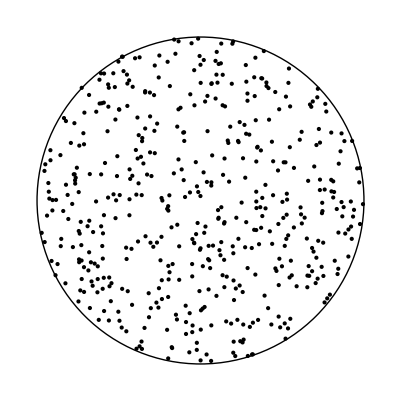

```mathematica
Graphics[ {Map[ Point, t1], Circle[]}]
```

Sitten satunnaissuunta johon pallotaso käännetään

```mathematica
v1 = SphereRandomSample[1, 3, "r"->1][[1]]
```

{-0.873759,0.08954,0.478046}

```mathematica
tf = RotationTransform[ {{0,0,1},v1}]
```

TransformationFunction[(0.483471 | 0.0529323 | -0.873759 | 0.
0.0529323 | 0.994576 | 0.08954 | 0.
0.873759 | -0.08954 | 0.478046 | 0.
0. | 0. | 0. | 1.)]

```mathematica
tf[{0,0,1}]
```

{-0.873759,0.08954,0.478046}

```mathematica
t1[[1]]
tf[{t1[[1,1]],t1[[1,2]],0}]
```

{-0.68775,-0.160417}

{-0.340998,-0.195951,-0.586563}

```mathematica
roc = Map[ tf[ {#[[1]],#[[2]],0}] &, t1];
```

```mathematica
Graphics3D[ {Map[ Point, roc], Arrow[ {{0,0,0},v1}]}]
```

-Graphics3D-

Symbolisesti kiertomatriisi on

```mathematica
t = RotationTransform[ {{0,0,1},{v[1],v[2],v[3]}}];
```

```mathematica
t1 = Simplify[ Simplify[t[[1]]], Assumptions:>{{v[1],v[2],v[3]} ∈ Reals}]
```

{{(v[2]^2+(v[1]^2 v[3])/(√(v[1]^2+v[2]^2+v[3]^2)))/(v[1]^2+v[2]^2),(v[1] v[2] (-1+v[3]/(√(v[1]^2+v[2]^2+v[3]^2))))/(v[1]^2+v[2]^2),v[1]/(√(v[1]^2+v[2]^2+v[3]^2)),0},{(v[1] v[2] (-1+v[3]/(√(v[1]^2+v[2]^2+v[3]^2))))/(v[1]^2+v[2]^2),(v[1]^2+(v[2]^2 v[3])/(√(v[1]^2+v[2]^2+v[3]^2)))/(v[1]^2+v[2]^2),v[2]/(√(v[1]^2+v[2]^2+v[3]^2)),0},{-v[1]/(√(v[1]^2+v[2]^2+v[3]^2)),-v[2]/(√(v[1]^2+v[2]^2+v[3]^2)),v[3]/(√(v[1]^2+v[2]^2+v[3]^2)),0},{0,0,0,1}}

```mathematica
Map[ FortranForm, Flatten[t1]] //TableForm
```

(v(2)**2 + (v(1)**2*v(3))/Sqrt(v(1)**2 + v(2)**2 + v(3)**2))/(v(1)**2 + v(2)**2)
(v(1)*v(2)*(-1 + v(3)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2)))/(v(1)**2 + v(2)**2)
v(1)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2)
0
(v(1)*v(2)*(-1 + v(3)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2)))/(v(1)**2 + v(2)**2)
(v(1)**2 + (v(2)**2*v(3))/Sqrt(v(1)**2 + v(2)**2 + v(3)**2))/(v(1)**2 + v(2)**2)
v(2)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2)
0
-(v(1)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2))
-(v(2)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2))
v(3)/Sqrt(v(1)**2 + v(2)**2 + v(3)**2)
0
0
0
0
1

Suoran etäisyys pisteestä. Ulkopuolelle siirretty pallo on pisteessä shp(li), sisällä sph(lj). Suuntavektori on dir1, joten toinen suoran virittävä piste on sph(li)-dir1

```mathematica
Clear[sph]
x1 = {sph[li,1],sph[li,2],sph[li,3]}
x2 = x1-{dir1[1],dir1[2],dir1[3]}
x0 = {sph[lj,1],sph[lj,2],sph[lj,3]}
```

{sph[li,1],sph[li,2],sph[li,3]}

{-dir1[1]+sph[li,1],-dir1[2]+sph[li,2],-dir1[3]+sph[li,3]}

{sph[lj,1],sph[lj,2],sph[lj,3]}

Etäisyyden neliö on: t1/t2, jossa t1=

```mathematica
t1 = FullSimplify[ Total[ Cross[ x2-x1, x1-x0]^2]]
```

(dir1[2] (sph[li,1]-sph[lj,1])+dir1[1] (-sph[li,2]+sph[lj,2]))^2+(dir1[3] (sph[li,1]-sph[lj,1])+dir1[1] (-sph[li,3]+sph[lj,3]))^2+(dir1[3] (sph[li,2]-sph[lj,2])+dir1[2] (-sph[li,3]+sph[lj,3]))^2

```mathematica
t2 = Total[ (x2-x1)^2]
```

dir1[1]^2+dir1[2]^2+dir1[3]^2

```mathematica
FortranForm[ t1]
```

(dir1(2)*(sph(li,1) - sph(lj,1)) + dir1(1)*(-sph(li,2) + sph(lj,2)))**2 + 
     -  (dir1(3)*(sph(li,1) - sph(lj,1)) + dir1(1)*(-sph(li,3) + sph(lj,3)))**2 + 
     -  (dir1(3)*(sph(li,2) - sph(lj,2)) + dir1(2)*(-sph(li,3) + sph(lj,3)))**2

```mathematica
FortranForm[t2]
```

dir1(1)**2 + dir1(2)**2 + dir1(3)**2